# h=√12 QR=1/(√12)(I+C+C^2)(1+D+D^2+D^3)

Computation of the sequences  of the roots, ratios, ||m_n||, and sum of the alphas using m:=(m_n) , tables, graphs, for the paper
“COMPUTATIONAL EXPLORATIONS OF THE THOMPSON GROUP T FOR THE AMENABILITY PROBLEM OF F” 
by S. Haagerup, U. Haagerup, M. Ramirez-Solano:

```mathematica
m={1/4,1,6,42,318,2528,20790,175344,1508158,13177554,116636378,1043596346,9423929906,85780131568,786252907282,7251162207110,67241091321510,626619942680948,5865627675769158,55130780282172364,520110723876289138,4923701716098043110,46759540919860581346,445382340814268264936,4253954798148920432622,40735421620966779279998,391022235546378412228050,3761992784005490950198026,36271465945557216051920334}
Ntuple=Length[m]-1
```

{1/4,1,6,42,318,2528,20790,175344,1508158,13177554,116636378,1043596346,9423929906,85780131568,786252907282,7251162207110,67241091321510,626619942680948,5865627675769158,55130780282172364,520110723876289138,4923701716098043110,46759540919860581346,445382340814268264936,4253954798148920432622,40735421620966779279998,391022235546378412228050,3761992784005490950198026,36271465945557216051920334}

28

```mathematica
(*mm=Riffle[0Range[Length[m]],m]
Table[d[n]=Det[Table[If[i+j==0,1,mm⟦i+j⟧],{i,0,n},{j,0,n}]],{n,0,Length[m]}]
d[-1]=1;
Table[k[n]=(d[n-1]/d[n])^(1/2),{n,0,Length[m]}]
Table[α[n]=k[n-1]/k[n],{n,1,Length[m]}]*)
```

```mathematica
(*G is called D in the paper*)
G=Table[0,{k,0,Ntuple}]
For[k=0,k≤Ntuple,k++,
mtx=DiagonalMatrix[Table[0,{i,0,k}]];
n=Length[mtx];
Table[If[1≤ Min[{i+j,i-j}]&& Max[{i+j,i-j}]≤n,mtx⟦i+j,i-j⟧=m⟦i⟧,0],{i,0,n},{j,0,n}];
Table[If[1≤ Min[{i-j,i+j}]&& Max[{i-j,i+j}]≤n,mtx⟦i-j,i+j⟧=m⟦i⟧,0],{i,0,n},{j,0,n}];
If[k<6,Print["det G[",k,"]=",Det[mtx],",   ","G[",k,"]=",mtx//MatrixForm]];
G⟦k+1⟧=Det[mtx];
]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

det G[0]=1/4,   G[0]=(1/4)

det G[1]=1/4,   G[1]=(1/4 | 0
0 | 1)

det G[2]=1/2,   G[2]=(1/4 | 0 | 1
0 | 1 | 0
1 | 0 | 6)

det G[3]=3,   G[3]=(1/4 | 0 | 1 | 0
0 | 1 | 0 | 6
1 | 0 | 6 | 0
0 | 6 | 0 | 42)

det G[4]=36,   G[4]=(1/4 | 0 | 1 | 0 | 6
0 | 1 | 0 | 6 | 0
1 | 0 | 6 | 0 | 42
0 | 6 | 0 | 42 | 0
6 | 0 | 42 | 0 | 318)

det G[5]=1368,   G[5]=(1/4 | 0 | 1 | 0 | 6 | 0
0 | 1 | 0 | 6 | 0 | 42
1 | 0 | 6 | 0 | 42 | 0
0 | 6 | 0 | 42 | 0 | 318
6 | 0 | 42 | 0 | 318 | 0
0 | 42 | 0 | 318 | 0 | 2528)

```mathematica
PrependTo[G,1];
G
```

{1,1/4,1/4,1/2,3,36,1368,103512,24054736,11370578336,17207989120192,53622388668128640,513772187250632248320,10174573070219686619334656,640010618296391589025140030464,84745451237271880290944771899928576,34817450647721644223232564069400738570240,30127002340841493712345091256089474310253404160,81881261014876463622825364538038810782314802049335296,472740814277803278026377768336168310240410063680118116286464,8526768067430487135806173644029280682024032672920330436556289212416,328902200124160581777401401765740193470667801510137256171711551651999383552,39718208028086122818537790112314185241591364989992155176583640544280517243421327360,10277749771067773894433420014516877932591610776224252696534527967155540086277841908819558400,8309249036664849713462121734614661973553075194682532205642844976142640453765243639397256399814656000,14497538614870768617655632925508726698714280239623169274361248061868691537180622746049914871197423955607552000,79160847522744446745591968983505414822312008758485507464035440990888854807984562222702068384382874779423789221203148800,934079058690169701061380960868270255233430913691170464247565457251989251515390925333523155479555946710342862452268582439925841920,34455479248455165183913626268602262421351793726604572761970251094363126242209197205602899612719070559650531294325071838246405327779826499584,2766406763332459812785521681664289377544624812376376822944525980452246578610801460049194094364855920226956623196407054448360112863595405832562451415040}

```mathematica
Table[(GG[(k-1)+2]GG[(k+1)+2])/GG[(k)+2]^2,{k,0,Length[G]*0+10-3}]
```

{(GG[1] GG[3])/GG[2]^2,(GG[2] GG[4])/GG[3]^2,(GG[3] GG[5])/GG[4]^2,(GG[4] GG[6])/GG[5]^2,(GG[5] GG[7])/GG[6]^2,(GG[6] GG[8])/GG[7]^2,(GG[7] GG[9])/GG[8]^2,(GG[8] GG[10])/GG[9]^2}

```mathematica
(*α^2=a2. *)
a2=Table[(G⟦(k-1)+2⟧G⟦(k+1)+2⟧)/G⟦(k)+2⟧^2,{k,0,Length[G]-3}]
a2//N
```

{4,2,3,2,19/6,227/114,13246/4313,3058107/1503421,1137622531/355330573,553628723205/268874830003,1288085191077932/418924911469755,4148124624547871777/2006922606447782220,63120671961419081422965/19872213027772825428388,1315665406149477856324233896/625010369430069911157363311,128391951274282158141421961753945/41379614861949160298312876904262,17902570846189146051201561759005557229/8500354162041417046687637712256039690,11551426690027001631418783087114459841766382/3677612590434752650432750397471859657013355,10616333633922414876844900988562781807560450849285/4997635559990018531666587191042407884662768679769,45070869722427118348825202790066660354938279224581207668/14426904732598976990551079355962167670910951650394229623,139121900291213449902880933661421512109162681237386248564634789/65054077662891289793443097259744878250305425055849688999605478,981990766827719070143032479156303548617157942020908275609167971205380/313665580867920476701165582433452790709178735265862709209167052890777,16233241689441104188101847378967056235479069164645559823362917674532721401801/7575646978013252795894201300108754204099915502546721492115715130668738793072,1224936172923186986155972418465109400095318283231045455761074314448841513327374635071/392065039484702068116509247379946820548691206978769405232792967497083285761941601136,684054362119795717315420414058155214697119598579976780511475143737536439167269294031904999712/316972695795625675714955205330454329435465820109654701448167609258370988989457841468706375115,865382321348431634750807810567746272648726586176709202260885636022388645210235259714032753614600489828/276518604562201855042565020094084295248303990166152368056511842000364142173397498055456445144604186165,543808894469725030782718118869975872691210156178076046738017667070555301219001806074040972668175609726698531231/251645557157975663330052595086114930541712470876329763616038770646695629145255286606795210470780928228453919796,234406009021525185607874014630366216385527518816593604512083908636935958435996942735862564490460591515791830392774162027/74983771697452951445834882401317880228587747317867284210247259529511073744689649631160128837447049779148845355700851084,4104815132361477523834261188038331561192864601940102124411185465604688297224095272131417716066115352759729061741774610782358952300/1885864647539038806136406829129580209042403855961138265190387839148038359833880079766984792272308452926858358930790054253332396391}

{4.,2.,3.,2.,3.16667,1.99123,3.07118,2.0341,3.20159,2.05906,3.07474,2.06691,3.17633,2.10503,3.10278,2.1061,3.14101,2.12427,3.12408,2.13856,3.13069,2.14282,3.12432,2.15809,3.12956,2.16101,3.12609,2.17662}

{2,√2,√3,√2,√(19/6),√(227/114),√(13246/4313),√(3058107/1503421),√(1137622531/355330573),√(553628723205/268874830003),2 √(322021297769483/418924911469755),(√(4148124624547871777/501730651611945555))/2,(√(63120671961419081422965/4968053256943206357097))/2,2 √(328916351537369464081058474/625010369430069911157363311),√(128391951274282158141421961753945/41379614861949160298312876904262),√(17902570846189146051201561759005557229/8500354162041417046687637712256039690),√(11551426690027001631418783087114459841766382/3677612590434752650432750397471859657013355),√(10616333633922414876844900988562781807560450849285/4997635559990018531666587191042407884662768679769),2 √(11267717430606779587206300697516665088734569806145301917/14426904732598976990551079355962167670910951650394229623),√(139121900291213449902880933661421512109162681237386248564634789/65054077662891289793443097259744878250305425055849688999605478),2 √(245497691706929767535758119789075887154289485505227068902291992801345/313665580867920476701165582433452790709178735265862709209167052890777),(√(16233241689441104188101847378967056235479069164645559823362917674532721401801/473477936125828299743387581256797137756244718909170093257232195666796174567))/4,(√(1224936172923186986155972418465109400095318283231045455761074314448841513327374635071/24504064967793879257281827961246676284293200436173087827049560468567705360121350071))/4,4 √(42753397632487232332213775878634700918569974911248548781967196483596027447954330876994062482/316972695795625675714955205330454329435465820109654701448167609258370988989457841468706375115),6 √(24038397815234212076411328071326285351353516282686366729469045445066351255839868325389798711516680273/276518604562201855042565020094084295248303990166152368056511842000364142173397498055456445144604186165),(√(543808894469725030782718118869975872691210156178076046738017667070555301219001806074040972668175609726698531231/62911389289493915832513148771528732635428117719082440904009692661673907286313821651698802617695232057113479949))/2,(41 √(139444383712983453663220710666487933602336418094344797449187334108825674262936908230733232891410226957639399400817467/18745942924363237861458720600329470057146936829466821052561814882377768436172412407790032209361762444787211338925212771))/2,(10 √(41048151323614775238342611880383315611928646019401021244111854656046882972240952721314177160661153527597290617417746107823589523/124652300055458973239236355947490264329592428842695370823609481072644481448468509469692960028574820075805298362799263285962879))/123}

{2.,1.41421,1.73205,1.41421,1.77951,1.41111,1.75248,1.42622,1.7893,1.43494,1.75349,1.43767,1.78223,1.45087,1.76147,1.45124,1.77229,1.45749,1.76751,1.46238,1.76938,1.46384,1.76757,1.46904,1.76906,1.47004,1.76808,1.47534}

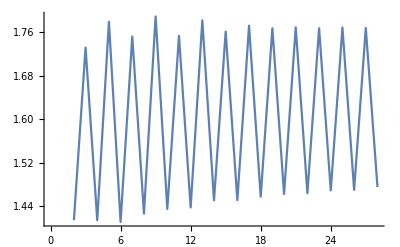

```mathematica
a=Table[Sqrt[a2⟦i⟧],{i,1,Length[a2]}]
a//N
ListPlot[Table[{i,a⟦i⟧},{i,2,Ntuple}],Joined->True]
```

```mathematica
MnormFunctiontest=Function[n,Module[{i,j,eigenvalues,A},
A=Table[0,{i,1,n+1},{j,1,n+1}];
Table[A⟦i,i+1⟧=a⟦i⟧^2,{i,1,n}];
Table[A⟦i+1,i⟧=1,{i,1,n}];
A
]];
Table[(MnormFunctiontest[i]//MatrixForm),{i,0,7}]
MnormFunction=Function[n,Module[{i,j,eigenvalues,A},
A=Table[0,{i,1,n+1},{j,1,n+1}];
Table[A⟦i,i+1⟧=a⟦i⟧^2,{i,1,n}];
Table[A⟦i+1,i⟧=1,{i,1,n}];
eigenvalues=Eigenvalues[A];
eigenvalues=eigenvalues//N;
Max[eigenvalues]
]];
Table[Mnorm[i]=MnormFunction[i],{i,0,Ntuple}]
```

{(0),(0 | 4
1 | 0),(0 | 4 | 0
1 | 0 | 2
0 | 1 | 0),(0 | 4 | 0 | 0
1 | 0 | 2 | 0
0 | 1 | 0 | 3
0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0
0 | 1 | 0 | 3 | 0
0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0 | 0
0 | 1 | 0 | 3 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0
0 | 0 | 0 | 1 | 0 | 19/6
0 | 0 | 0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 3 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0
0 | 0 | 0 | 1 | 0 | 19/6 | 0
0 | 0 | 0 | 0 | 1 | 0 | 227/114
0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 19/6 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 227/114 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 13246/4313
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{0.,2.,2.44949,2.71519,2.82843,2.9224,2.97266,3.01653,3.04235,3.06842,3.08578,3.10309,3.11454,3.12665,3.13534,3.14458,3.15121,3.15841,3.16373,3.16956,3.17394,3.1788,3.18249,3.1866,3.18976,3.19332,3.19607,3.19917,3.2016}

```mathematica
(*renaming a to α *)
Table[α[n]=a⟦n⟧,{n,1,Length[a]}];
```

{2.,1.41421,1.73205,1.41421,1.77951,1.41111,1.75248,1.42622,1.7893,1.43494,1.75349,1.43767,1.78223,1.45087,1.76147,1.45124,1.77229,1.45749,1.76751,1.46238,1.76938,1.46384,1.76757,1.46904,1.76906,1.47004,1.76808,1.47534}

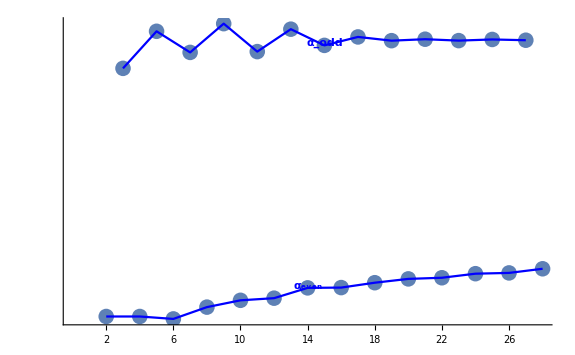

```mathematica
Table[α[n],{n,1,Ntuple}]//N
Show[
ListPlot[Table[{i,α[i]},{i,2,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i]},{i,2,Ntuple,2}],Joined->True,PlotStyle->{Blue}],ListPlot[Table[{i,α[i]},{i,3,Ntuple,2}],Joined->True,PlotStyle->{Blue}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[α, even]],Large,Bold],{14,.002+α[14]}]}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[α, odd]],Large,Bold],{15,.003+α[15]}]}]
]
```

```mathematica
(*ma_0=m_1 ... ma_Ntuple=m_Length[m] ma_28=m_29*)
```

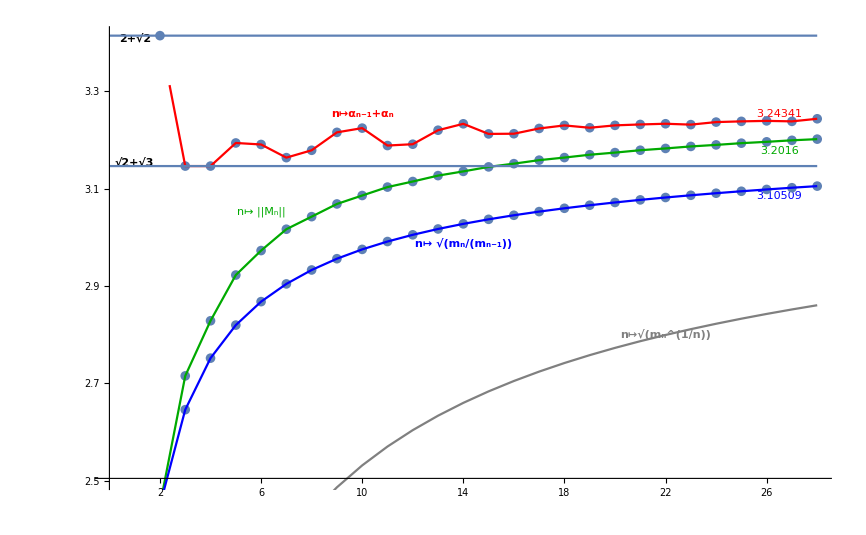

```mathematica
Table[ma[i-1]=m⟦i⟧,{i,1,Length[m]}];
Show[
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Ticks->{Range[2,Ntuple,2],Range[2.5,4.2,.1]},PlotStyle->{PointSize[.008]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{2.5,Sqrt[6+4 √2]}],
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Joined->True,PlotStyle->{Darker[Green]}],
Graphics[{Darker[Green],Text[Style[HoldForm["n↦ ||M_n||"],Large],{6,.08+Mnorm[6]}]}],
Graphics[{Darker[Green],Text[Style[N[Mnorm[Ntuple],6],Large],{Ntuple-1.5,-.025+Mnorm[Ntuple]}]}],
Graphics[{Red,Text[Style[N[α[Ntuple-1]+α[Ntuple],6],Large],{Ntuple-1.5,.01+α[Ntuple-1]+α[Ntuple]}]}],
Graphics[{Blue,Text[Style[N[(ma[Ntuple]/ma[Ntuple-1])^(1/2),6],Large],{Ntuple-1.5,-.02+(ma[Ntuple]/ma[Ntuple-1])^(1/2)}]}],
Plot[8,{x,0,Ntuple}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotStyle->{PointSize[.008]}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Blue}],
Graphics[{Blue,Text[Style[HoldForm[n↦(Subscript[m, n]/Subscript[m, n-1])^(1/2)],Large,Bold],{14,-.04+(ma[14]/ma[13])^(1/2)}]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple}],PlotStyle->{PointSize[.008]},Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Red}],
Graphics[{Red,Text[Style[HoldForm[n↦Subscript[α, n-1]+Subscript[α, n]],Large,Bold],{10,.03+α[9]+α[10]}]}],
ListPlot[Table[{i,(ma[i]^(1/i))^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Gray}],
Graphics[{Gray,Text[Style[HoldForm[n↦√((Subscript[m, n])^(1/n))],Large,Bold],{22,-.00+(ma[22]^(1/(2 22)))}]}],
Graphics[{Black,Text[Style[HoldForm["√2+√3"],Medium,Bold],{1,Sqrt[2]+Sqrt[3]+.007}]}],
Graphics[{Black,Text[Style[HoldForm["2+√2"],Medium,Bold],{1,Sqrt[2]+2-.007}]}],
Plot[Sqrt[2]+Sqrt[3],{x,0,Ntuple}],
Plot[2+Sqrt[2],{x,0,Ntuple}]

]
```

```mathematica
Grid[Transpose[
{Range[Ntuple],
N[Table[(ma[i]^(1/i))^(1/2),{i,1,Ntuple,1}],6],
N[Table[(ma[i]/ma[i-1])^(1/2),{i,1,Ntuple}],6],
N[Table[α[n],{n,1,Ntuple}],6],
N[Table[Mnorm[i],{i,1,Ntuple}],6],
N[Table[α[i-1]+α[i],{i,1,Ntuple}],6]}
],Alignment->Left]
```

1 | 1. | 2. | 2. | 2. | 2.+α[0]
2 | 1.56508 | 2.44949 | 1.41421 | 2.44949 | 3.41421
3 | 1.86441 | 2.64575 | 1.73205 | 2.71519 | 3.14626
4 | 2.05496 | 2.75162 | 1.41421 | 2.82843 | 3.14626
5 | 2.18916 | 2.81952 | 1.77951 | 2.9224 | 3.19373
6 | 2.28992 | 2.86773 | 1.41111 | 2.97266 | 3.19062
7 | 2.36899 | 2.90414 | 1.75248 | 3.01653 | 3.16359
8 | 2.43306 | 2.93277 | 1.42622 | 3.04235 | 3.1787
9 | 2.48626 | 2.95593 | 1.7893 | 3.06842 | 3.21552
10 | 2.53129 | 2.97509 | 1.43494 | 3.08578 | 3.22424
11 | 2.57 | 2.99123 | 1.75349 | 3.10309 | 3.18844
12 | 2.60371 | 3.00504 | 1.43767 | 3.11454 | 3.19117
13 | 2.63339 | 3.01701 | 1.78223 | 3.12665 | 3.2199
14 | 2.65975 | 3.02753 | 1.45087 | 3.13534 | 3.2331
15 | 2.68337 | 3.03685 | 1.76147 | 3.14458 | 3.21234
16 | 2.70467 | 3.04518 | 1.45124 | 3.15121 | 3.21271
17 | 2.72399 | 3.0527 | 1.77229 | 3.15841 | 3.22353
18 | 2.74163 | 3.05953 | 1.45749 | 3.16373 | 3.22978
19 | 2.7578 | 3.06577 | 1.76751 | 3.16956 | 3.225
20 | 2.7727 | 3.0715 | 1.46238 | 3.17394 | 3.22989
21 | 2.78647 | 3.07679 | 1.76938 | 3.1788 | 3.23176
22 | 2.79926 | 3.08169 | 1.46384 | 3.18249 | 3.23321
23 | 2.81116 | 3.08625 | 1.76757 | 3.1866 | 3.23141
24 | 2.82228 | 3.09051 | 1.46904 | 3.18976 | 3.23662
25 | 2.83269 | 3.09449 | 1.76906 | 3.19332 | 3.2381
26 | 2.84247 | 3.09824 | 1.47004 | 3.19607 | 3.23909
27 | 2.85168 | 3.10176 | 1.76808 | 3.19917 | 3.23811
28 | 2.86036 | 3.10509 | 1.47534 | 3.2016 | 3.24341